```mathematica
f=(a*x^3+b*x^2+c*x+d);
g=(q*(x-x1-λu/2)+r*(x-x1-λu/2)^3)*Exp[-p*(x-x1-λu/2)];
gii=(ⅇ^(1/2 p (2 x1-2 xt+λu)) (48 r-24 p r (2 x1-2 xt+λu)-p^3 (2 x1-2 xt+λu) (4 q+r (2 x1-2 xt+λu)^2)+p^2 (8 q+6 r (2 x1-2 xt+λu)^2)))/(8 p^4);

Simplify[f/.x->x1]
Simplify[D[f, x]/.x->x1]
Simplify[f/.x->(x1+λu/2)]
Simplify[∫_x1^(x1+λu/2) fⅆx]
Simplify[∫_(x1+λu/2)^(+∞) gⅆx]
∫_x1^(x1+λu/2) Simplify[∫_x1^xt fⅆx]ⅆxt

Simplify[g/.x->(x1+λu/2)]
Simplify[D[f, x]/.x->(x1+λu/2)]
Simplify[D[g, x]/.x->(x1+λu/2)]
Simplify[∫_xt^(+∞) gⅆx]
Simplify[∫_(x1+λu/2)^(+∞) giiⅆxt]
```

d+x1 (c+x1 (b+a x1))

c+x1 (2 b+3 a x1)

d+1/8 (2 x1+λu) (4 c+(2 x1+λu) (2 b+2 a x1+a λu))

1/192 λu (96 d+96 b x1^2+96 a x1^3+48 b x1 λu+72 a x1^2 λu+8 b λu^2+24 a x1 λu^2+3 a λu^3+24 c (4 x1+λu))

If[Re[p]>0,(p^2 q+6 r)/p^4,Integrate[ⅇ^(1/2 p (-2 x+2 x1+λu)) (q (x-x1-λu/2)+r (x-x1-λu/2)^3),{x,x1+λu/2,∞},Assumptions→Re[p]≤0]]

(d λu^2)/8+1/8 c x1 λu^2+1/8 b x1^2 λu^2+1/8 a x1^3 λu^2+(c λu^3)/48+1/24 b x1 λu^3+1/16 a x1^2 λu^3+(b λu^4)/192+1/64 a x1 λu^4+(a λu^5)/640

0

c+b (2 x1+λu)+3/4 a (2 x1+λu)^2

q

If[Re[p]>0,(ⅇ^(1/2 p (2 x1-2 xt+λu)) (48 r-24 p r (2 x1-2 xt+λu)-p^3 (2 x1-2 xt+λu) (4 q+r (2 x1-2 xt+λu)^2)+p^2 (8 q+6 r (2 x1-2 xt+λu)^2)))/(8 p^4),Integrate[ⅇ^(1/2 p (-2 x+2 x1+λu)) (q (x-x1-λu/2)+r (x-x1-λu/2)^3),{x,xt,∞},Assumptions→Re[p]≤0]]

If[Re[p]>0,16 p q+(192 r)/p,Integrate[ⅇ^(1/2 p (2 x1-2 xt+λu)) (48 r-24 p r (2 x1-2 xt+λu)-p^3 (2 x1-2 xt+λu) (4 q+r (2 x1-2 xt+λu)^2)+p^2 (8 q+6 r (2 x1-2 xt+λu)^2)),{xt,x1+λu/2,∞},Assumptions→Re[p]≤0]]/(8 p^4)

```mathematica
Solve[{
d+x1 (c+x1 (b+a x1))==0,
c+x1 (2 b+3 a x1)==(B0*2*π)/λu,
d+1/8 (2 x1+λu) (4 c+(2 x1+λu) (2 b+2 a x1+a λu))==0,
1/192 λu (96 d+96 b x1^2+96 a x1^3+48 b x1 λu+72 a x1^2 λu+8 b λu^2+24 a x1 λu^2+3 a λu^3+24 c (4 x1+λu))==(3*λu*B0)/(4*π),
(p^2 q+6 r)/p^4==(-λu*B0)/(4*π),
(d λu^2)/8+1/8 c x1 λu^2+1/8 b x1^2 λu^2+1/8 a x1^3 λu^2+(c λu^3)/48+1/24 b x1 λu^3+1/16 a x1^2 λu^3+(b λu^4)/192+1/64 a x1 λu^4+(a λu^5)/640+(2 p^2 q+24 r)/p^5==0
q==c+b (2 x1+λu)+3/4 a (2 x1+λu)^2,


},{a,b,c,d,q,p}]
```

```mathematica
{{q->(2 B0 (-18+π^2))/(π λu),d->-(2 (-72 B0 x1^3+8 B0 π^2 x1^3-36 B0 x1^2 λu+6 B0 π^2 x1^2 λu+B0 π^2 x1 λu^2))/(π λu^3),p->-(√(144-8 π^2))/λu,c->(2 (-216 B0 x1^2+24 B0 π^2 x1^2-72 B0 x1 λu+12 B0 π^2 x1 λu+B0 π^2 λu^2))/(π λu^3),b->-(12 (-36 B0 x1+4 B0 π^2 x1-6 B0 λu+B0 π^2 λu))/(π λu^3),a->(16 B0 (-9+π^2))/(π λu^3)},
{q->(2 B0 (-18+π^2))/(π λu),d->-(2 (-72 B0 x1^3+8 B0 π^2 x1^3-36 B0 x1^2 λu+6 B0 π^2 x1^2 λu+B0 π^2 x1 λu^2))/(π λu^3),p->(√(144-8 π^2))/λu,c->(2 (-216 B0 x1^2+24 B0 π^2 x1^2-72 B0 x1 λu+12 B0 π^2 x1 λu+B0 π^2 λu^2))/(π λu^3),b->-(12 (-36 B0 x1+4 B0 π^2 x1-6 B0 λu+B0 π^2 λu))/(π λu^3),a->(16 B0 (-9+π^2))/(π λu^3)}}
```

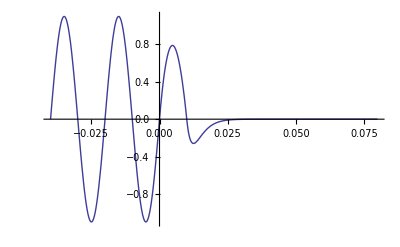

```mathematica
B0=1.1;
λu=0.02;
x1=0;
p=(√(144-8 π^2))/λu;
q=(2 B0 (-18+π^2))/(π λu);
a=(16 B0 (-9+π^2))/(π λu^3);
b=-(12 B0 (4 (-9+π^2) x1+(-6+π^2) λu))/(π λu^3);
c=(2 B0 (24 (-9+π^2) x1^2+12 (-6+π^2) x1 λu+π^2 λu^2))/(π λu^3);
d=-(2 B0 x1 (2 x1+λu) (4 (-9+π^2) x1+π^2 λu))/(π λu^3);

FF[x_]:=If[x<x1,B0*Sin[(2*π)/λu*x],If[x<x1+λu/2,a*x^3+b*x^2+c*x+d,q*(x-x1-λu/2)*Exp[-p*(x-x1-λu/2)]]];

Plot[FF[x],{x,-2*λu,4*λu},PlotRange->All]
```

```mathematica
f=(a*x^3+b*x^2+c*x+d);
g=(q*(x-x1+λu/2)+r*(x-x1+λu/2)^3)*Exp[-p*(x-x1+λu/2)];
gi=(ⅇ^(p (x1-xt-λu/2)) (-48 r+24 p r (2 x1-2 xt-λu)+p^3 (2 x1-2 xt-λu) (4 q+r (-2 x1+2 xt+λu)^2)-2 p^2 (4 q+3 r (-2 x1+2 xt+λu)^2)))/(8 p^4);

Simplify[f/.x->x1]
Simplify[D[f, x]/.x->x1]
Simplify[f/.x->(x1-λu/2)]
Simplify[∫_(x1-λu/2)^x1 fⅆx]
Simplify[∫_(-∞)^(x1-λu/2) gⅆx]
∫_(x1-λu/2)^x1 Simplify[∫_(x1-λu/2)^xt fⅆx]ⅆxt

Simplify[g/.x->(x1-λu/2)]
Simplify[D[f, x]/.x->(x1-λu/2)]
Simplify[D[g, x]/.x->(x1-λu/2)]
Simplify[∫_(-∞)^xt gⅆx]
Simplify[∫_(-∞)^(x1-λu/2) giⅆxt]
```

d+x1 (c+x1 (b+a x1))

c+x1 (2 b+3 a x1)

d+c (x1-λu/2)+b (x1-λu/2)^2+a (x1-λu/2)^3

1/192 λu (96 d+96 c x1+96 b x1^2+96 a x1^3-24 c λu-48 b x1 λu-72 a x1^2 λu+8 b λu^2+24 a x1 λu^2-3 a λu^3)

If[Re[p]<0,-(p^2 q+6 r)/p^4,Integrate[ⅇ^(-1/2 p (2 x-2 x1+λu)) (q (x-x1+λu/2)+r (x-x1+λu/2)^3),{x,-∞,x1-λu/2},Assumptions→Re[p]≥0]]

(d λu^2)/8+1/8 c x1 λu^2+1/8 b x1^2 λu^2+1/8 a x1^3 λu^2-(c λu^3)/24-1/12 b x1 λu^3-1/8 a x1^2 λu^3+(b λu^4)/64+3/64 a x1 λu^4-(a λu^5)/160

0

c+b (2 x1-λu)+3 a (x1-λu/2)^2

q

If[Re[p]<0,(ⅇ^(p (x1-xt-λu/2)) (-48 r+24 p r (2 x1-2 xt-λu)+p^3 (2 x1-2 xt-λu) (4 q+r (-2 x1+2 xt+λu)^2)-2 p^2 (4 q+3 r (-2 x1+2 xt+λu)^2)))/(8 p^4),Integrate[ⅇ^(-1/2 p (2 x-2 x1+λu)) (q (x-x1+λu/2)+r (x-x1+λu/2)^3),{x,-∞,xt},Assumptions→Re[p]≥0]]

If[Re[p]<0,16 p q+(192 r)/p,Integrate[ⅇ^(p (x1-xt-λu/2)) (-48 r+24 p r (2 x1-2 xt-λu)+p^3 (2 x1-2 xt-λu) (4 q+r (-2 x1+2 xt+λu)^2)-2 p^2 (4 q+3 r (-2 x1+2 xt+λu)^2)),{xt,-∞,x1-λu/2},Assumptions→Re[p]≥0]]/(8 p^4)

```mathematica
Solve[{
d+x1*(c+x1*(b+a*x1))==0,
c+x1 (2 b+3 a x1)==(B0*2*π)/λu,
d+c (x1-λu/2)+b (x1-λu/2)^2+a (x1-λu/2)^3==0,
1/192 λu (96 d+96 c x1+96 b x1^2+96 a x1^3-24 c λu-48 b x1 λu-72 a x1^2 λu+8 b λu^2+24 a x1 λu^2-3 a λu^3)==(-3*λu*B0)/(4*π),
-(p^2 q+6 r)/p^4==(λu*B0)/(4*π),
(d λu^2)/8+1/8 c x1 λu^2+1/8 b x1^2 λu^2+1/8 a x1^3 λu^2-(c λu^3)/24-1/12 b x1 λu^3-1/8 a x1^2 λu^3+(b λu^4)/64+3/64 a x1 λu^4-(a λu^5)/160+(2 p^2 q+24 r)/p^5==0,
q==c+b (2 x1-λu)+3 a (x1-λu/2)^2
},{a,b,c,d,q,r,p},WorkingPrecision->MachinePrecision]
```

{{r→(11.315 B0)/λu^3,q→-(5.17597 B0)/λu,d→(0.5 B0 x1 (-12.5664-(8.85772 x1^2)/λu^2+(29.5616 x1)/λu))/λu,c→(B0 (6.28319+(13.2866 x1^2)/λu^2-(29.5616 x1)/λu))/λu,b→(0.5 B0 (29.5616-(26.5732 x1)/λu))/λu^2,a→(4.42886 B0)/λu^3,p→4.26855/λu},{r→((26.8133-29.2252 ⅈ) B0)/λu^3,q→-(5.17597 B0)/λu,d→(0.5 B0 x1 (-12.5664-(8.85772 x1^2)/λu^2+(29.5616 x1)/λu))/λu,c→(B0 (6.28319+(13.2866 x1^2)/λu^2-(29.5616 x1)/λu))/λu,b→(0.5 B0 (29.5616-(26.5732 x1)/λu))/λu^2,a→(4.42886 B0)/λu^3,p→-(4.85349-4.22828 ⅈ)/λu},{r→((26.8133+29.2252 ⅈ) B0)/λu^3,q→-(5.17597 B0)/λu,d→(0.5 B0 x1 (-12.5664-(8.85772 x1^2)/λu^2+(29.5616 x1)/λu))/λu,c→(B0 (6.28319+(13.2866 x1^2)/λu^2-(29.5616 x1)/λu))/λu,b→(0.5 B0 (29.5616-(26.5732 x1)/λu))/λu^2,a→(4.42886 B0)/λu^3,p→-(4.85349+4.22828 ⅈ)/λu}}

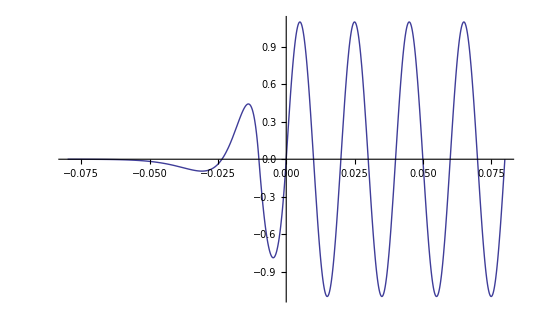

NIntegrate::nlim: xx = xx is not a valid limit of integration.

NIntegrate::inumr: The integrand NIntegrate[FFR[xx], {xx, -4 λu, xx}] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-0.08`, -0.079`}}.

NIntegrate::nlim: xx = xx is not a valid limit of integration.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

NIntegrate::inumr: The integrand NIntegrate[FFR[xx], {xx, -4 λu, xx}] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-0.08`, -0.078`}}.

NIntegrate::inumr: The integrand NIntegrate[FFR[xx], {xx, -4 λu, xx}] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-0.08`, -0.077`}}.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

NIntegrate::write: Tag Times in -xx is Protected.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

-Graphics-

```mathematica
B0=1.1;
λu=0.02;
x1=0;

p=4.268551117903719/λu; (*(√(144-8 π^2))/λu;*)
q=-(5.175970595436878 B0)/λu;(*(2 B0 (-18+π^2))/(π λu);*)
r=(11.315030268114286 B0)/λu^3;
a=(4.428858846970832 B0)/λu^3;(*(16 B0 (-9+π^2))/(π λu^3);*)
b=(0.5 B0 (29.561600075689178-(26.57315308182499 x1)/λu))/λu^2;(*(12 B0 (-4 (-9+π^2) x1+(-6+π^2) λu))/(π λu^3);*)
c=(B0 (6.283185307179586+(13.286576540912495 x1^2)/λu^2-(29.561600075689178 x1)/λu))/λu; (*(2 B0 (24 (-9+π^2) x1^2-12 (-6+π^2) x1 λu+π^2 λu^2))/(π λu^3);*)
d=(0.5 B0 x1 (-12.566370614359172-(8.857717693941664 x1^2)/λu^2+(29.561600075689178 x1)/λu))/λu;

FFR[x_]:=If[x<x1-λu/2,(q*(x-x1+λu/2)+r*(x-x1+λu/2)^3)*Exp[p*(x-x1+λu/2)],If[x<x1,a*x^3+b*x^2+c*x+d,B0*Sin[(2*π)/λu*x]]];
I1FF[x_]:=NIntegrate[FFR[xx],{xx,-4*λu,x}];
I2FF[x_]:=NIntegrate[I1FF[xx],{xx,-4*λu,x}];

Plot[FFR[x],{x,-4*λu,4*λu},PlotRange->All]
ListPlot[Table[{x,I2FF[x]},{x,-4*λu,4*λu,λu/20.}],PlotRange->All,Joined->True]
```

```mathematica
CForm[q*(x-x1+λu/2)*Exp[p*(x-x1+λu/2)]]
```

(2*B0*Power(E,(Sqrt(144 - 8*Power(Pi,2))*(x - x1 + λu/2.))/λu)*(-18 + Power(Pi,2))*(x - x1 + λu/2.))/(Pi*λu)

```mathematica
N[Pi]
```

3.14159

```mathematica
3.141592653589793
```

```mathematica
N[-((17280-960 π^2)/(54-π^2))^(1/3)]
```

-5.61326